```mathematica
Quit[];
```

```mathematica
Install["/Path/To/HiggsTools/build/wstp/MHiggsTools"];
HBInitialize["/Path/To/HBDataSet"];
```

------------------------------------------------------------------------------

HiggsTools 1.0

H. Bahl, P. Bechtle, T. Biekoetter, S. Heinmeyer, S. Paasch,

C. Li, G. Weiglein, J. Wittbrodt

------------------------------------------------------------------------------

```mathematica
HPAddParticle["h",125.09,"neutral","even"];
HPAddParticle["H",500,"neutral","even"];

HPEffectiveCouplingInput["h",uuRe->1,ddRe->1,ssRe->1,ccRe->1,ttRe->1,bbRe->1,eeRe->1,mumuRe->1,tautauRe->1,WW->1,ZZ->1,gamgam->1,gg->1,Zgam->1,calcggH->False,calcHgamgam->False];

HPSetDecayWidth["H","h","h",1];
HPSetCxn["H","LHC13","ggH",1];
```

```mathematica
evalPoint[mass_]:=(
HPSetMass["H",mass];
HBApplyBounds[];
{mass,HBGetAppliedBounds[]}
);
```

```mathematica
res=Table[evalPoint[mass],{mass,250,2000,10}];
```

```mathematica
HlimitQ=MemberQ[contributingParticles/.#,"H"]&/@Flatten[res[[;;,2,;;,-1]]];
limitIDs=(limitID/.#)&/@Flatten[res[[;;,2,;;,1]]];
limitIDs=DeleteDuplicates@Pick[limitIDs,HlimitQ];
Length@limitIDs
```

17

```mathematica
selectLim[list_,id_]:=Select[list,TrueQ[id==limitID/.#]&];
getobsRatio[list_,id_]:=Module[{sel=selectLim[list,id]},
If[sel=={},
Infinity,
obsRatio/.sel[[1]]
]
];
getExclusion[limitID_]:=Module[{},
Map[{#[[1]],1/getobsRatio[#[[2]],limitID]}&,res]
];
```

```mathematica
exclusionLimits={#,getExclusion[#]}&/@limitIDs;
```

```mathematica
genLabel[limitid_]:=Module[{info,exp,proc},
info=Select[limits,limitid==id/.#&];
exp=ToString[(experiment/.info)[[1]]];
proc=ToString[(process/.info)[[1]]];
exp<>" "<>proc
];
genLineStyle[limitid_]:=Module[{info,exp,proc},
info=Select[limits,limitid==id/.#&];
exp=ToString[(experiment/.info)[[1]]];
If[exp=="ATLAS",
Solid,
Dashed
]
];
```

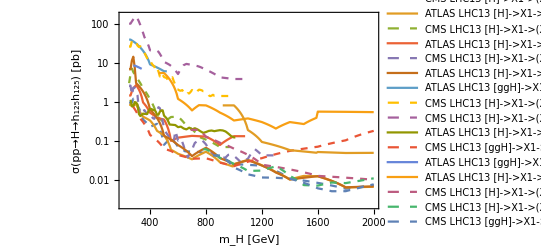

```mathematica
ListLogPlot[exclusionLimits[[;;,2]],PlotRange->All,Joined->True,PlotLegends->Map[genLabel,limitIDs],PlotStyle->Map[genLineStyle,limitIDs],Frame->True,FrameLabel->{"m_H [GeV]","σ(pp→H→h_125h_125) [pb]"}]
```